```mathematica
Clear["`*" ]
```

# 1d Schrodinger equation.

### Introduction

Based on just an easy Google search,  it is not too hard to find the solution for the time-independent Simple Harmonic Oscillator.  The potential energy for a harmonic Oscillator in 1D is just

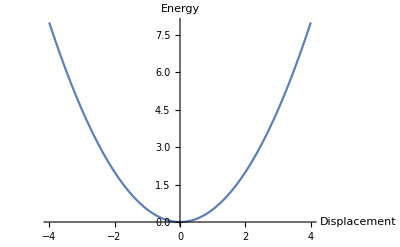

```mathematica
PEParabola[x_]:=1/2 k x^2 /.{k->1};
PEGraph = Plot[PEParabola[x],{x,-4,4}, AxesLabel->{"Displacement","Energy "},AspectRatio->GoldenRatio^-1]
```

Where we’ve set k =1 for convenience.
The full time depentent schreding equation for one dimension , where ψ is the wave equation looks like this:

```mathematica
TimeDependent = -ℏ^2/(2 m) D[ψ[x,t],{x,2}]+U[x]ψ[x,t] == I ℏ D[ψ[x,t],t]
```

U[x] ψ[x,t]-(ℏ^2 ψ^(2,0)[x,t])/(2 m)==ⅈ ℏ ψ^(0,1)[x,t]

Where U[x] is the potential energy, so for the SHO, we have U = PEParabola.
For convenience and readability, we will set ℏ and m equal to 1.

```mathematica
ConvenientTimeDependent = TimeDependent /.{U->PEParabola,ℏ->1,m->1}
```

1/2 x^2 ψ[x,t]-1/2 ψ^(2,0)[x,t]==ⅈ ψ^(0,1)[x,t]

### Time independent

Because the Time dependant is still so hairy, we will look just at 
the time independant. It looks like this

```mathematica
TimeIndependent =  -ℏ^2/(2 m) ψ''[x]+U[x]ψ[x] == energy ψ[x]
```

U[x] ψ[x]-(ℏ^2 ψ''[x])/(2 m)==energy ψ[x]

Where once again we will put in our beutifying variables:

```mathematica
ConvenientTimeIndependent =  TimeIndependent/.{U->PEParabola,ℏ->1,m->1,k->1}
```

1/2 x^2 ψ[x]-ψ''[x]/2==energy ψ[x]

At this point, I would suggest plugging in to DSolve, but after spending a few hours trying to figure out why the boundary conditions couldn’t be met,  we’ll jump ahead to the solution

```mathematica
ψ[n_,x_] = √(1/(2^n n!))((m ω)/(π ℏ))^(1/4)Exp[(-m ω x^2)/(2 ℏ)]HermiteH[n,√((m ω)/ℏ)x]
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4) √(2^-n/(n!)) HermiteH[n,x √((m ω)/ℏ)])/π^(1/4)

Let’s clean up some of our constants, and then plot the n=0 and n=1 energy level.

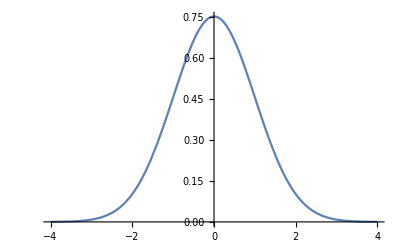

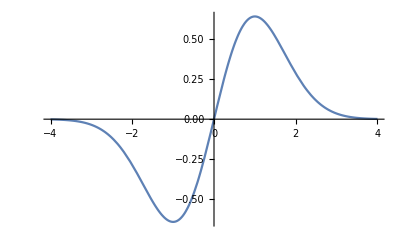

```mathematica
ψc[x_,n_] = ψ[x,n]/.{m->1,ω->1,ℏ->1};
Plot[ψc[0,x],{x,-4,4}]
Plot[ψc[1,x],{x,-4,4}]
```

Now, to show the simple elegence of these solutions, we’ll plot them over the potential energy graph. We’ll overlay energy level “n” with the y axis for effect.

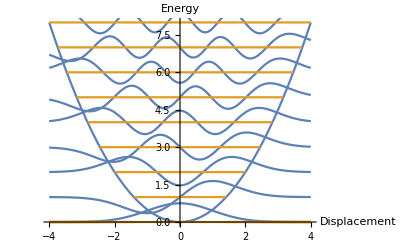

```mathematica
Show[PEGraph,Table[Plot[{ψc[n,x]+n,If[Abs[x]<√(2n),n,0]},{x,-4,4}],{n,0,8}]]
```

Now, because we usually want probability density, and this was a little messy, we will square the wave functions.

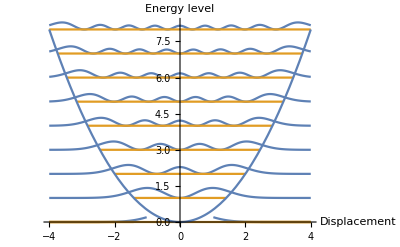

```mathematica
Show[Table[Plot[{ψc[n,x]^2+n,If[Abs[x]<√(2n),n,0]},{x,-4,4}],{n,0,8}],PEGraph,PlotRange->All,AxesLabel->{"Displacement","Energy level "},AspectRatio->GoldenRatio^-1]
```

Notice how the number of nodes (or minima, in the case of ψ^2) is exactly equal to the energy level number.